### Background

This notebook owes a great deal to “Delta-Sigma Modulators: Modeling, Design, and Applications” by Bourdopoulos, Pnevmatikakis, Anastassopoulos, and Deliyannis (“BPAD” below).

### Linear Circuits

#### Filters

An electronic filter may be represented by its impulse response, which in a discrete time system must be bounded in amplitide and causal. In a bounded time system, the time bounds also apply to the impulse response: there are no input samples before the beginning of time for it to respond to, and no output samples after the end of time for it to produce.

If we know the Z transform of the filter response, we may in these restricted circumstances obtain the impulse response from the coefficients of its Taylor series in Z^-1, avoiding the need to compute a complete inverse Z transform:

```mathematica
zToImpulse[tf_,z_Symbol,n_Integer]:=CoefficientList[Series[tf/.z->zz^-1,{zz,0,n-1}],zz]
```

Here's a simple low-pass filter with a time constant of 1 step:

```mathematica
lpfi=zToImpulse[1/(1-(1/ⅇ)z^-1),z,10]
```

{1,1/ⅇ,1/ⅇ^2,1/ⅇ^3,1/ⅇ^4,1/ⅇ^5,1/ⅇ^6,1/ⅇ^7,1/ⅇ^8,1/ⅇ^9}

A filter convolves its impulse response with the signal. In matrix form, this implies a shift of each succesive row by 1, with the rows reproducing the impulse response:

```mathematica
impulseToOperator[x_List,n_Integer]:=Table[PadRight[x,n,0,i],{i,0,n-1}]
```

```mathematica
(lpfo=impulseToOperator[lpfi,10])//MatrixForm
```

(1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3 | 1/ⅇ^4 | 1/ⅇ^5 | 1/ⅇ^6 | 1/ⅇ^7 | 1/ⅇ^8 | 1/ⅇ^9
0 | 1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3 | 1/ⅇ^4 | 1/ⅇ^5 | 1/ⅇ^6 | 1/ⅇ^7 | 1/ⅇ^8
0 | 0 | 1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3 | 1/ⅇ^4 | 1/ⅇ^5 | 1/ⅇ^6 | 1/ⅇ^7
0 | 0 | 0 | 1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3 | 1/ⅇ^4 | 1/ⅇ^5 | 1/ⅇ^6
0 | 0 | 0 | 0 | 1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3 | 1/ⅇ^4 | 1/ⅇ^5
0 | 0 | 0 | 0 | 0 | 1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3 | 1/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/ⅇ | 1/ⅇ^2 | 1/ⅇ^3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/ⅇ | 1/ⅇ^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/ⅇ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### Modulators

The word "modulator" has a couple of different meetings in this context. Here, I just mean a device that multiplies a variable signal by a fixed but time-dependent "carrier" function (not a ΔΣ "modulator" whose model here is a "filter").  The operator representing a modulator is simply a diagonal matrix with the "carrier's" time series on the diagonal. Here's a modulator that zeros the first 5 samples of 10:

```mathematica
modo[c_]:=DiagonalMatrix[c]
```

```mathematica
modo[{0,0,0,0,0,1,1,1,1,1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### Noise

Noise is represented by a "covariance matrix", where the [[i,j]] element is the expectation value of the product of sample i with sample j.

#### Random Bias

"kTC" noise in a CCD pixel is an example of a random bias: it's constant within a pixel, but is unknown and variable between pixels. Since it is constant, its covariances are all equal, and it is therefore represented by a constant matrix. The covariance matrix for unit random bias is simply:

```mathematica
ktcCov[n_]:=ConstantArray[1,{n,n}]
```

```mathematica
ktcCov[6]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1)

#### White noise

Samples of white noise are uncorrelated with each other, and have constant variance, so the covariance matrix for unit white noise is simply an identity matrix:

```mathematica
whiteCov[n_]:=IdentityMatrix[n]
```

```mathematica
whiteCov[6]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

#### Flicker Noise

Start with the autocorrelation function for flicker noise, which is just the inverse Fourier transform of its 1/ω power spectrum:

```mathematica
flickacf=Apart[InverseFourierTransform[Abs[1/ω],ω,t]]
```

-√(2/π) (EulerGamma+Log[Abs[t]])

The constant "EulerGamma" is physically meaningless, as it corresponds to a constant offset. And for CCD signal processing purposes, we'll want to adjust the normalization.

It is convenient to take the "differential averaging" function as the normalization device. This averages the "reset level" for a time tint and subtracts that from the average of the "signal level" for the same time: it's equivalent to integrating the product of the signal with:

```mathematica
da[tint_,t_]:=Piecewise[{{-1,-tint<t<0},{1,0<t<tint}},0]/tint
```

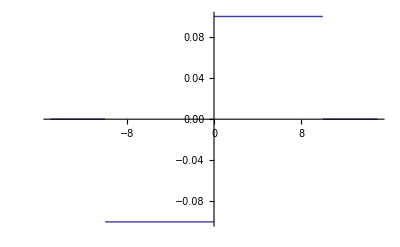

```mathematica
Plot[da[10,t],{t,-15,15}]
```

The flicker noise variance through the differential averaging filter is just the integral of the noise power that gets through. That, in turn, is just the product of the flicker noise power density with the power response of the filter:

```mathematica
daft=FourierTransform[da[tint,t],t,ω,Assumptions->tint>0]
```

-(ⅈ ⅇ^(-ⅈ tint ω) (-1+ⅇ^(ⅈ tint ω))^2)/(√(2 π) tint ω)

```mathematica
dapd=Simplify[ComplexExpand[daft Conjugate[daft]]]
```

(8 Sin[(tint ω)/2]^4)/(π tint^2 ω^2)

```mathematica
flicknorm=Integrate[Abs[1/ω] dapd,{ω,-∞,∞},Assumptions->tint>0]
```

(2 Log[4])/π

This result is independent of tint, reproducing the common result that the readout noise of a CCD whose noise is dominated by flicker noise is independent of the pixel sampling time.

Now, we need to sample the normalized flickacf to get an approximation of the discrete-time ACF. But there's a problem: a logarithmic divergence at lag zero, related to the logarithmic divergence in total noise power with increasing frequency. But this is unphysical: there must be a bandwidth limit, and in a sampled system that limit should be small enough to prevent aliasing, implying that the correlation at lag zero should be only modestly above the correlation at lag one. Any reasonable video filter is going to strongly suppress noise on a time scale shorter than the pixel time, so the exact value we use for lag zero doesn't matter as long as it's larger than the lag one value. Inspection shows that for nonzero integral lags, flickacf is negative:

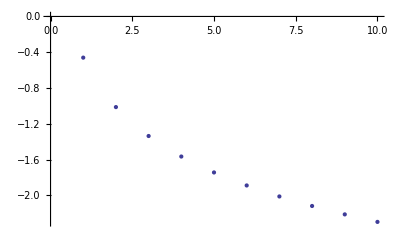

```mathematica
ListPlot[Table[flickacf,{t,1,10}]]
```

We therefore define:

```mathematica
flick[0]=0;
flick[tt_Integer]:=flick[tt]=N[(flickacf/flicknorm/.t->tt)]
```

(Using a value cache to avoid expensive recomputation)

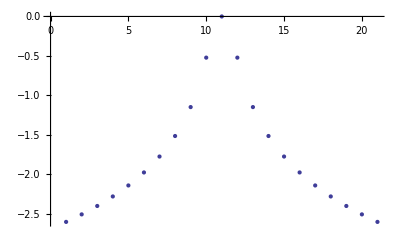

```mathematica
ListPlot[Table[flick[t],{t,-10,10}]]
```

This still isn't physically reasonable: all the values are <=0, an impossiblity for an ACF. The lag zero value must not only be larger than the other values, it must be larger in absolute magnitude. Whatever we do to correct for this, it will depend on the length of the finite piece of ACF we need, because of the logarithmic divergence with increasing lag. It's physically sensible to add enough constant covariance (random DC offset) when we construct the covariance matrix to make the covariance positive at all scales. Remember that, by definition, the covariance matrix for a signal with a time-independent expectation for its ACF is just a matrix whose rows are the ACF with lag zero on the diagonal.

```mathematica
flickCov[n_Integer]:=Table[N[flick[i-j]-flick[n]],{i,0,n-1},{j,0,n-1}]
flickCov[6]//MatrixForm
```

(2.14173 | 1.61989 | 0.993228 | 0.626657 | 0.366571 | 0.164832
1.61989 | 2.14173 | 1.61989 | 0.993228 | 0.626657 | 0.366571
0.993228 | 1.61989 | 2.14173 | 1.61989 | 0.993228 | 0.626657
0.626657 | 0.993228 | 1.61989 | 2.14173 | 1.61989 | 0.993228
0.366571 | 0.626657 | 0.993228 | 1.61989 | 2.14173 | 1.61989
0.164832 | 0.366571 | 0.626657 | 0.993228 | 1.61989 | 2.14173)

#### Filtered Noise

Given a covariance matrix and a filter operator, the following transformation yields the covariance of the filtered noise (mathematical justification needed!). The vector variant is for decimation filters, whose operators are vectors and thus cannot be transposed in Mathematica's model of linear algebra:

```mathematica
filtNoise[ filt_/;MatrixQ[filt],noise_]:=Transpose[filt].noise.filt
filtNoise[ filt_/;VectorQ[filt],noise_]:=filt.noise.filt
```

### ΔΣ modulator

Fourth order “CIDIDF” archictecture, see BPAD Fig. 3.7.

Delay and integrate functions in z space.

```mathematica
delay[x_]:= x z^-1
integrate[x_]:=x/(1-z^-1);
```

```mathematica
filter= out/.Solve[{q1==integrate[j1 in+k1 fb-g1 delay[q2]],
q2==integrate[c1 q1+j2 in+k2 fb],
q3==integrate[c2 q2+j3 in+k3 fb-g2 delay[q4]],
q4==integrate[c3 q3+j4 in+k4 fb],
out==delay[q4]},out,{q1,q2,q3,q4}][[1]]
```

-(-(c2 c3 (-(in j2)/(1-1/z)-(fb k2)/(1-1/z)+(c1 (-(in j1)/(1-1/z)-(fb k1)/(1-1/z)))/(1-1/z)))/((1-1/z)^2 z)-((-(in j4)/(1-1/z)-(fb k4)/(1-1/z)+(c3 (-(in j3)/(1-1/z)-(fb k3)/(1-1/z)))/(1-1/z)) (1+(c1 g1)/((1-1/z)^2 z)))/z)/((1+(c1 g1)/((1-1/z)^2 z)) (-1-(c3 g2)/((1-1/z)^2 z)))

Temporary assumptions. The c coefficients are essentially free at this level of analysis: we’ll choose them later to match the integrator voltage swings to the available dynamic range. Eventually, we’ll optimize the j coefficients for best SNR from a CCD signal contaminated by 1/f noise.

```mathematica
tempa={c1->1,c2->1,c3->1,j1->k1,j2->k2,j3->k3,j4->k4}
```

{c1→1,c2→1,c3→1,j1→k1,j2→k2,j3→k3,j4→k4}

```mathematica
ffb=Cancel[(filter/.tempa/.in->0)/fb]
```

(-k4+k3 z+3 k4 z-g1 k4 z-k2 z^2-2 k3 z^2+g1 k3 z^2-3 k4 z^2+g1 k4 z^2+k1 z^3+k2 z^3+k3 z^3+k4 z^3)/((1-2 z+g1 z+z^2) (1-2 z+g2 z+z^2))

To get the NTF, we need to know the effective noise gain, ke. From BPAD eq. 4.12b, it’s the “cross power” between the comparator output and the filter output, divided by the filter output power. But this is tricky: the relationship between the comparator output voltage and the voltages in the filter is arbitrary. 

It is convenient here to work in charge units, where “1” is the maximum charge we want to see on an integrator, and a comparator output of “1” corresponds to 1 charge unit. Then, a comparator output of 0 corresponds to -1 charge unit. The actual feedback charge to each stage is then determined by multiplying the negated comparator output by the “k” coefficients we’ll derive below.

We assume a Gaussian distribution for the charge on the final filter stage. Then, define a parameter σi that gives the desired standard deviation of that distribution. This should be fairly small, but not too small (we want the voltage range to match the available dynamic range).

The “cross power” above is then just the integrator charge times 1 or -1, depending on its sign. It’s thus the average absolute value of the integrator charge. Define the “Gaussian Mean Absolute Deviation”:

```mathematica
gmad=Integrate[2PDF[NormalDistribution[0,1]][x]x,{x,0,∞}]
```

√(2/π)

Then, ke is:

```mathematica
ke=σi gmad/σi^2
```

(√(2/π))/σi

```mathematica
ntf=Together[1/(1+ke ffb)]
```

((1-2 z+g1 z+z^2) (1-2 z+g2 z+z^2) σi)/(-k4 √(2/π)+k3 √(2/π) z+3 k4 √(2/π) z-g1 k4 √(2/π) z-k2 √(2/π) z^2-2 k3 √(2/π) z^2+g1 k3 √(2/π) z^2-3 k4 √(2/π) z^2+g1 k4 √(2/π) z^2+k1 √(2/π) z^3+k2 √(2/π) z^3+k3 √(2/π) z^3+k4 √(2/π) z^3+σi-4 z σi+g1 z σi+g2 z σi+6 z^2 σi-2 g1 z^2 σi-2 g2 z^2 σi+g1 g2 z^2 σi-4 z^3 σi+g1 z^3 σi+g2 z^3 σi+z^4 σi)

Design parameters

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->25};
```

First, we find g1 and g2, since they depend only on the desired zero locations. In BPAD, the optimum zero frequencies in the z plane are parameterized by angles ϑn. These are bandwidth independent. To get the actual angles ϕn, they must be multiplied by Pi/oversamp. The actual zero frequencies are then Exp[±I ϕn]. It’s not clear exactly what the oversampling ratio, oversamp, should be here, so some optimization will be needed.

```mathematica
g12=(Solve[b CoefficientList[Numerator[ntf/.param],z]==Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],{g1,g2},{b}]//Quiet)[[1]]
```

{g1→0.0018252,g2→0.0116978}

Now, find the main feedback coefficients.

```mathematica
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{k1→0.00609198,k2→0.022226,k3→0.121072,k4→0.366992}

### Modeling a Modulator Numerically

state[n, in, internal, out] represents the state of the modulator.
	n		timestep
	in		input value
	internal	list of intgrator states, of Length equal to modulator order
	out		output value

```mathematica
initState[f_,intern_List,out_Integer]=state[1,f[0],intern,out];
```

Bit to charge, charge to bit.

```mathematica
b2q[1]=1;
b2q[0]=-1;
q2b[x_]:=1/;x>0
q2b[x_]:=0/;x<=0
```

Extract the internal state of the modulator.

```mathematica
getIntern[state[_,_,i_List,_]]:=i
```

Nest the modulator function mod, with input f, n times

```mathematica
runMod[mod_, f_, init_, n_]:=NestList[mod[f],initState[f,init,0],n]
```

Constructor for a function we iterate to make a feedforward modulator. To make the function, feed it f and g12. f[n] is input for time step n, g12 is gain from integrator 1 to integrator 2.

```mathematica
modulator[in_][state[n_,v_,{q1_,q2_,q3_,q4_},out_]]:=
Module[{nq1,nq2,nq3,nq4,nv,fb},
fb=-b2q[out];
nv=in[n];
nq1=q1+j1 nv+k1 fb-g1 q2;
nq2=q2+j2 nv+k2 fb+c1 nq1;
nq3=q3+j3 nv+k3 fb+c2 nq2-g2 q4;
nq4=q4+j4 nv+k4 fb+c3 nq3;
state[n+1,nv,{nq1,nq2,nq3,nq4},q2b[nq4]]]/.tempa/.coeff/.g12
```

The first interesting thing to do is to run the modulator with a fixed input. A nice thing to plot is the trajectory of the internal state ("Poicaré diagram"). For some special inputs, we get limit cycling:

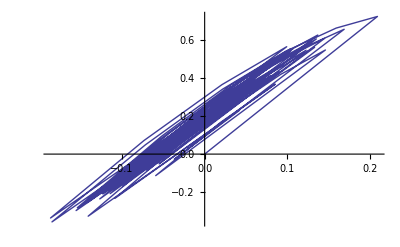

```mathematica
ListPlot[(getIntern/@runMod[modulator,(0.4)&,{0.,0.,0.,0.},100])[[All,{3,4}]],Joined->True]
```

#### Modeling an Input Signal

In these models, it turns out that a major computation burden is generating Gaussian random values. However, we don't need the high fidelity of Mathematica's generator here, so we'll use something really simple. The following function yields a random number with zero mean and unity variance, crudely Gaussian:

```mathematica
fastNoise=Compile[{},2.0 (RandomReal[]+RandomReal[]+RandomReal[]-1.5)];
```

Constructor for an input signal function. Parameters are kTC noise level, charge, random noise per sample, number of samples on charge (so pixel time is at least twice that). Yields 0.0 after the last sample.

```mathematica
sig[ktc_,chg_,noise_,samp_][n_]:=Piecewise[{{ktc+noise fastNoise[], n≤samp}, {ktc+noise fastNoise[]-chg, samp<n≤2 samp}, {0., True}}]
```

A nice noisy CCD pixel:

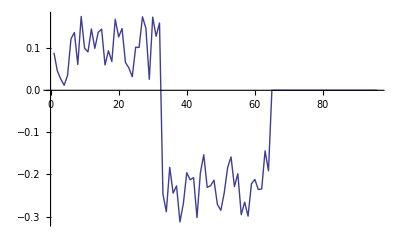

```mathematica
ListPlot[Table[sig[0.1,0.33,0.05,32][n],{n,1,96}],Joined->True]
```

#### Care and Feeding of the Modulator

Correlated double sampler function.

```mathematica
dcs[samp_][n_]:=Piecewise[{{-1., n≤samp}, {1., True}}]
```

Modulator input is product of the input signal with the correlated double sampler function.

```mathematica
inp[ktc_,chg_,noise_,samp_][n_]:= dcs[samp][n]sig[ktc,chg,noise,samp][n]
```

Extract the output bit from state.

```mathematica
getOut[state[_,_,_List,i_]]:=i
```

Do a test run. ktx is the RMS kTC noise, chx is the full charge range in units where absolute full scale for a DC level is ±1. Each run will use a kTC level chosen from a Gaussian distribution and a charge level chosen from a uniform distribution: if chx is 1, the charge range is ±0.5. noise represents the RMS of Gaussian random numbers added to each sample, mod is the modulator model, samp is the number of charge samples, and cyc is the total number of modulator cycles per pixel.

```mathematica
testrun[ktx_,chx_,noise_,mod_,samp_,cyc_]:=Module[{ktc=fastNoise[] ktx,chg=chx (RandomReal[]-0.5)},{ktc,chg,getOut/@runMod[mod,inp[ktc,chg,noise,samp],{0.,0.,0.,0.},cyc]}]
```

Simulate 4096 units full scale, kTC of 100 units, noise of 16 units/sample, 16 charge samples, 48 cycles to convert, 10000 runs.

```mathematica
run1=Table[testrun[100./4096,1.,16./4096.,modulator,16,48],{10000}];
```

#### Processing the Output

Grab the matrix of output bits from a set of runs, each row representing a conversion

```mathematica
bitmat[runs_]:=2.*N[Drop[runs[[All,3]],None,{1}]]-1.
```

Grab the corresponding charge.

```mathematica
chg[runs_]:=N[runs[[All,2]]]
```

Use the "normal matrix" method of least squares to find the best output filter.

```mathematica
bestFilt[runs_]:=Module[{a=bitmat[runs],b=chg[runs]},LinearSolve[Transpose[a].a,Transpose[a].b]]
```

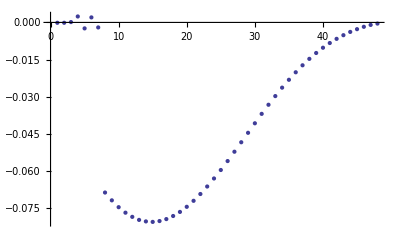

```mathematica
p1=ListPlot[filt1 = bestFilt[run1]]
```

#### Getting results

To apply the filter, just multiply the bit matrix with it (filter on the right). Thus, the following computes the residuals from a run:

```mathematica
resid[runs_,filt_]:=chg[runs]-bitmat[runs].filt
```

```mathematica
1./RootMeanSquare[resid[run1,filt1]]
```

677.595

Ideally, this would be (chx √(samp/2))/noise,or ~724 in this case. Thus, we see that digitization noise in this case is small: we have almost ideal performance! We can also examine the residuals in detail:

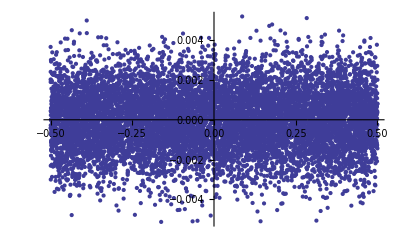

```mathematica
ListPlot[Transpose[{chg[run1],resid[run1,filt1]}],PlotRange->All]
```

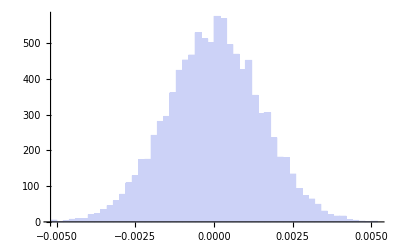

```mathematica
Histogram[resid[run1,filt1]]
```

Just for fun, try it without noise:

```mathematica
run2=Table[testrun[0.,1.,0.,modulator,16,48],{10000}];
```

```mathematica
1/RootMeanSquare[resid[run2,filt1]]
```

2249.04

Without noise, some evidence of nonlinearity, probably due to limit cycling.

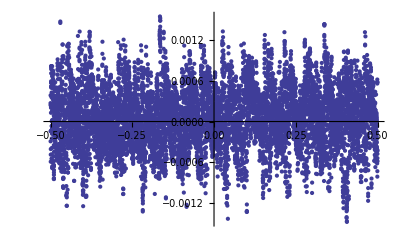

```mathematica
ListPlot[Transpose[{chg[run2],resid[run2,filt1]}],PlotRange->All]
```

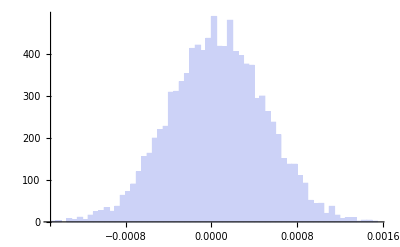

```mathematica
Histogram[resid[run2,filt1]]
```

```mathematica
run3=Table[testrun[0.,1.6,0.,modulator,16,48],{10000}];
```

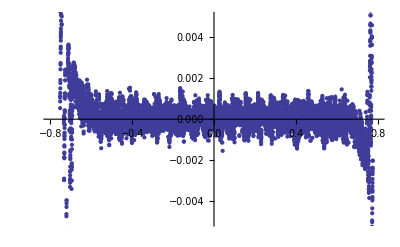

```mathematica
ListPlot[Transpose[{chg[run3],resid[run3,filt1]}],PlotRange->{-0.005,0.005}]
```

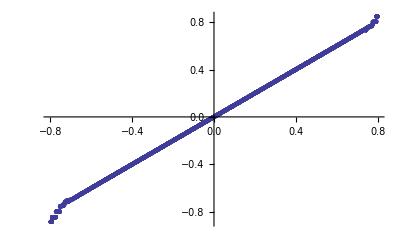

```mathematica
ListPlot[Transpose[{chg[run3],bitmat[run3].filt1}],PlotRange->All]
```

```mathematica
run6=Table[testrun[100./4096,1.,4./4096.,modulator,12,48],{10000}];
```

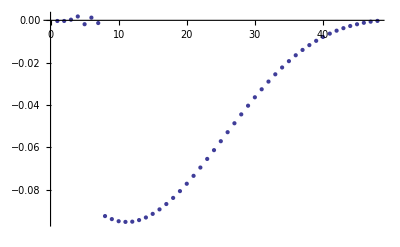

```mathematica
ListPlot[filt6 = bestFilt[run6]]
```

```mathematica
1/RootMeanSquare[resid[run6,filt6]]
```

1933.66

A bit better. Farther?

```mathematica
run7=Table[testrun[100./4096,1.,4./4096.,modulator,10,48],{10000}];
```

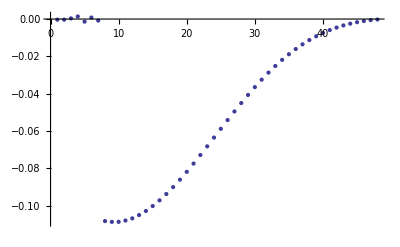

```mathematica
ListPlot[filt7 = bestFilt[run7]]
```

```mathematica
1/RootMeanSquare[resid[run7,filt7]]
```

1858.96

```mathematica
run8=Table[testrun[100./4096,1.,4./4096.,modulator,11,48],{10000}];
```

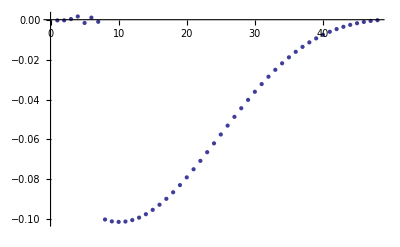

```mathematica
ListPlot[filt8 = bestFilt[run8]]
```

```mathematica
1/RootMeanSquare[resid[run8,filt8]]
```

1877.27

```mathematica
run9=Table[testrun[100./4096,1.,4./4096.,modulator,13,48],{10000}];
```

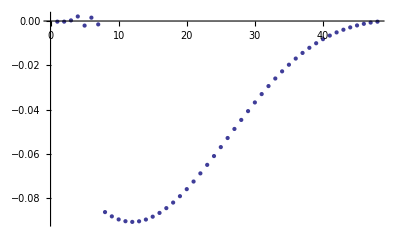

```mathematica
ListPlot[filt9 = bestFilt[run9]]
```

```mathematica
1/RootMeanSquare[resid[run9,filt9]]
```

1939.91

```mathematica
run10=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

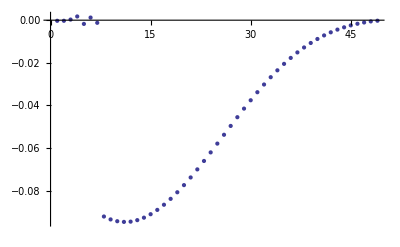

```mathematica
ListPlot[filt10 = bestFilt[run10]]
```

```mathematica
1/RootMeanSquare[resid[run10,filt10]]
```

3350.41

```mathematica
1.2%
```

4020.49

```mathematica
run10x=Table[testrun[100./4096,1.6,0.,modulator,12,49],{10000}];
```

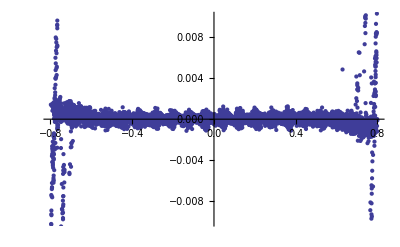

```mathematica
ListPlot[Transpose[{chg[run10x],resid[run10x,filt10]}],PlotRange->{-0.01,0.01}]
```

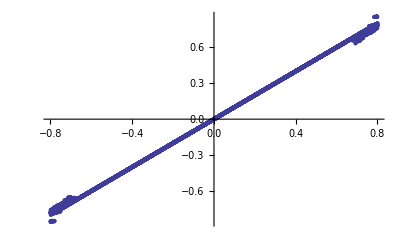

```mathematica
ListPlot[Transpose[{chg[run10x],bitmat[run10x].filt10}],PlotRange->All]
```

```mathematica
run11=Table[testrun[0.03,1.0,0.001,modulator,12,49],{10000}];
```

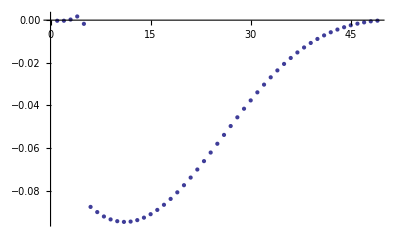

```mathematica
ListPlot[filt11 = bestFilt[run11]]
```

```mathematica
1/RootMeanSquare[resid[run11,filt11]]
```

1961.49

```mathematica
run11x=Table[testrun[0.03,1.6,0.001,modulator,12,49],{10000}];
```

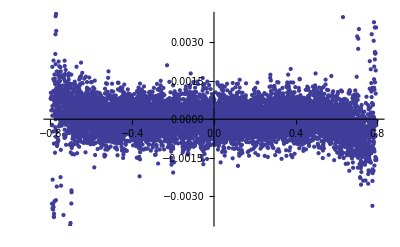

```mathematica
ListPlot[Transpose[{chg[run11x],resid[run11x,filt11]}],PlotRange->{-0.004,0.004}]
```

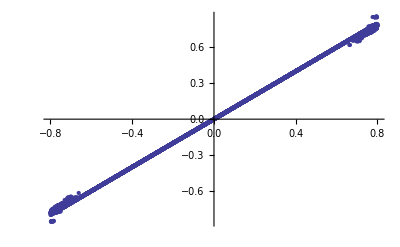

```mathematica
ListPlot[Transpose[{chg[run11x],bitmat[run11x].filt11}],PlotRange->All]
```

#### Optimizing the Zeros

Design parameters

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->20};
g12=(Solve[Take[b CoefficientList[Numerator[ntf/.param],z],3]==Take[Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],3],{g1,g2},{b}]//Quiet)[[1]]
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{g1→0.00285164,g2→0.0182677}

{k1→0.00596322,k2→0.021978,k3→0.118592,k4→0.366992}

```mathematica
run10v20=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

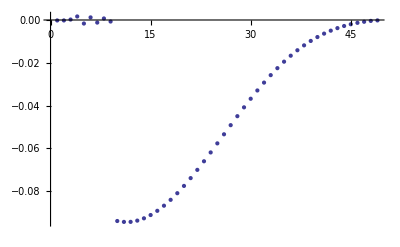

```mathematica
ListPlot[filt10v20 = bestFilt[run10v20]]
```

```mathematica
1/RootMeanSquare[resid[run10v20,filt10v20]]
```

2457.43

```mathematica
1.2%
```

2948.92

OK, reducing oversamp to 20 made it worse, try 30.

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->30};
g12=(Solve[Take[b CoefficientList[Numerator[ntf/.param],z],3]==Take[Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],3],{g1,g2},{b}]//Quiet)[[1]]
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{g1→0.00126756,g2→0.00812587}

{k1→0.00616194,k2→0.0223607,k3→0.12242,k4→0.366992}

```mathematica
run10v30=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

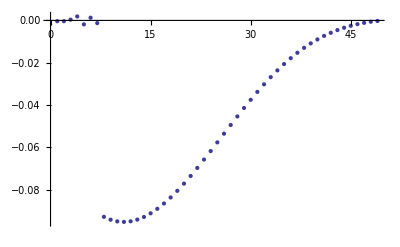

```mathematica
ListPlot[filt10v30 = bestFilt[run10v30]]
```

```mathematica
1/RootMeanSquare[resid[run10v30,filt10v30]]
```

3131.65

```mathematica
1.2%
```

3757.98

Looks like optimum is between 25 and 30?

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->27};
g12=(Solve[Take[b CoefficientList[Numerator[ntf/.param],z],3]==Take[Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],3],{g1,g2},{b}]//Quiet)[[1]]
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{g1→0.00156485,g2→0.0100303}

{k1→0.00612464,k2→0.0222889,k3→0.121701,k4→0.366992}

```mathematica
run10v27=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

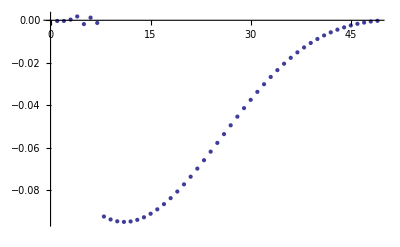

```mathematica
ListPlot[filt10v27 = bestFilt[run10v27]]
```

```mathematica
1/RootMeanSquare[resid[run10v27,filt10v27]]
```

3288.02

```mathematica
1.2%
```

3945.62

27 is almost the same as 25. 26?

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->26};
g12=(Solve[Take[b CoefficientList[Numerator[ntf/.param],z],3]==Take[Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],3],{g1,g2},{b}]//Quiet)[[1]]
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{g1→0.00168752,g2→0.010816}

{k1→0.00610925,k2→0.0222592,k3→0.121405,k4→0.366992}

```mathematica
run10v26=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

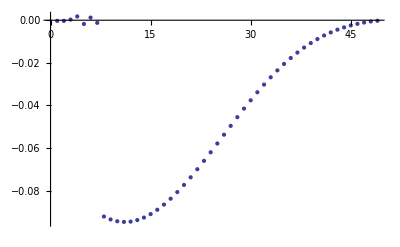

```mathematica
ListPlot[filt10v26 = bestFilt[run10v26]]
```

```mathematica
1/RootMeanSquare[resid[run10v26,filt10v26]]
```

3323.16

```mathematica
1.2%
```

3987.79

Maybe a bit below 25. 24?

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->24};
g12=(Solve[Take[b CoefficientList[Numerator[ntf/.param],z],3]==Take[Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],3],{g1,g2},{b}]//Quiet)[[1]]
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{g1→0.00198045,g2→0.0126918}

{k1→0.0060725,k2→0.0221885,k3→0.120697,k4→0.366992}

```mathematica
run10v24=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

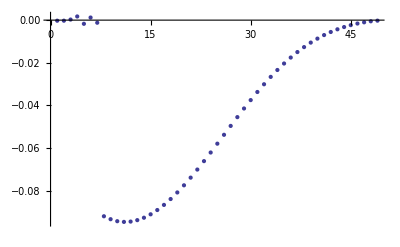

```mathematica
ListPlot[filt10v24 = bestFilt[run10v24]]
```

```mathematica
1/RootMeanSquare[resid[run10v24,filt10v24]]
```

3370.84

```mathematica
1.2%
```

4045.01

Best so far. 23?

```mathematica
param={ntfPoles -> {0.0365,0.7044,0.9361+I 0.2344,0.9361-I 0.2344},σi->0.3,ϑ1->0.34,ϑ2->0.8611,oversamp->23};
g12=(Solve[Take[b CoefficientList[Numerator[ntf/.param],z],3]==Take[Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],3],{g1,g2},{b}]//Quiet)[[1]]
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{g1→0.00215637,g2→0.0138182}

{k1→0.00605043,k2→0.022146,k3→0.120272,k4→0.366992}

```mathematica
run10v23=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

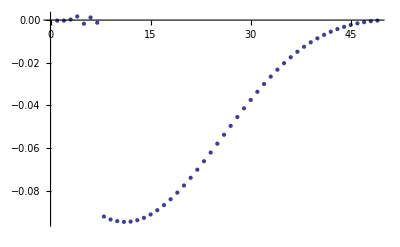

```mathematica
ListPlot[filt10v23 = bestFilt[run10v23]]
```

```mathematica
1/RootMeanSquare[resid[run10v23,filt10v23]]
```

3223.47

```mathematica
1.2%
```

3868.16

Bottom line: 25 was an excellent guess. The optimum is slightly lower, but SNR is more sensitive down there, so I think I’ll stick to 25.

#### Interstage gain optimization

```mathematica
Max/@Transpose[getIntern/@runMod[modulator,(0.6)&,{0.,0.,0.,0.},1000]]
```

{0.0122424,0.0554906,0.239024,0.99357}

```mathematica
Min/@Transpose[getIntern/@runMod[modulator,(0.6)&,{0.,0.,0.,0.},1000]]
```

{-0.0126378,-0.0590338,-0.281177,-0.354051}

```mathematica
Min/@Transpose[getIntern/@runMod[modulator,(-0.6)&,{0.,0.,0.,0.},1000]]
```

{-0.0102836,-0.0455606,-0.190646,-0.812355}

```mathematica
Max/@Transpose[getIntern/@runMod[modulator,(0.0)&,{0.,0.,0.,0.},1000]]
```

{0.00619477,0.0313867,0.15691,0.522412}

### Modeling the Delta-Sigma Chip with linear algebra

In the following, cyc is the total number of modulator cycles per pixel, samp is the number of samples for deintegration, and samp is also the number for integration.

```mathematica
cyc=49;
samp=12;
```

#### Premodulator

The premodulator gives the first samp cycles a weight of -1 (deintegration) the next samp cycles a weight of 1 (integration), and then continues with weight 0 until cyccycles have passed:

```mathematica
prefunc[n_Integer]:=Piecewise[{{-1,0<n≤ samp},{1,samp<n≤2samp}},0]
premod=Table[prefunc[n],{n,1,cyc}]
premodo=modo[premod];
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Delta-sigma modulator

We use a linear model for this. From previous work, the Z transforms of the signal and digitization noise transfer functions for our ASIC modulators are:

```mathematica
stfn=ks Cancel[(filter/.tempa/.fb->0)/in]/(1+ks Cancel[(filter/.tempa/.in->0)/fb])/.ks->ke/.param/.coeff/.g12
ntfn=ntf/.param/.coeff/.g12
```

(2.65962 (-0.366992+1.60292 z-2.46754 z^2+1.63615 z^3))/((1-2 z+z^2)^2 (1+(2.65962 (-0.366992+1.60292 z-2.46754 z^2+1.63615 z^3))/((1-2 z+z^2)^2)))

(2.12694 (4-8 z+4 z^2)^2)/(0.814786-25.1177 z+79.7706 z^2-88.9267 z^3+34.0311 z^4)

Impulse responses and filter operators are:

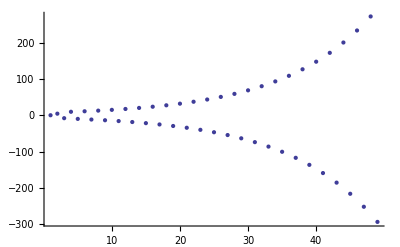

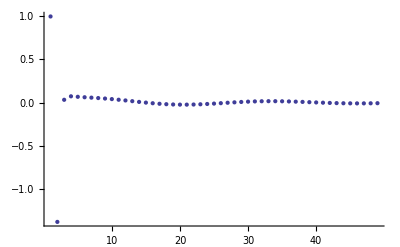

```mathematica
ListPlot[stfi=N[zToImpulse[stfn,z,cyc]],PlotRange->All]
stfo=impulseToOperator[stfi,cyc];
ListPlot[ntfi=N[zToImpulse[ntfn,z,cyc]],PlotRange->All]
ntfo=impulseToOperator[ntfi,cyc];
```

In the linear model of the ΔΣ modulator, we assume white noise filtered through the noise tranfer function represents the digitization noise at the modulator output:

```mathematica
onoise=filtNoise[ntfo,whiteCov[cyc]];
```

### Decimation

The "decimation filter" takes all of the samples from a pixel and yields a single number. Unlike the previous filters here, it is therefore just a vector, not a matrix. The signal to noise ratio for the filtered result is just the ratio of the modulator output signal dotted with the decimation filter and divided by the square root of the filtered variance (a scalar):

```mathematica
snr[ signal_,decimation_,covariance_]:=signal.decimation/Sqrt[filtNoise[decimation,covariance]]
```

A linear decimation filter will have optimum signal to noise if it is "matched" to the signal and noise in the modulator output. See:

http://en.wikipedia.org/wiki/Matched_filter

The matched filter is just the product of the inverse of the noise covariance matrix with the expected signal and a normalization constant, Here, we use LinearSolve to compute the matrix product because it's numerically more accurate than using the matrix inverse explicitly. The normalization is chosen to yield unit output for the input given by signal.

If you prefer, you can derive this from the single variable case of weighted least squares, see:

http://en.wikipedia.org/wiki/Weighted_least_squares#Weighted_least_squares

```mathematica
matched[signal_,covariance_]:=With[{h=LinearSolve[covariance,signal]},
h/(h.signal)]
```

### Making Decimation filters

Here's a theoretical CCD signal, just a step:

```mathematica
idealSignalFunc[n_Integer]:=Piecewise[{{1,samp<n}},0]
inputSignal=Table[idealSignalFunc[n],{n,1,cyc}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

That passes through the premodulator and the ΔΣ modulator to yield the following (average) signal:

```mathematica
signal=inputSignal.premodo.stfo;
```

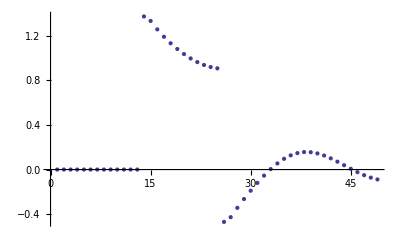

```mathematica
ListPlot[signal]
```

Make a mixture of white and kTC noise:

```mathematica
wktc= 0.0001*filtNoise[premodo.stfo,(ktcCov[cyc]+whiteCov[cyc])];
```

Make the matched decimation filter:

```mathematica
fwktc=matched[signal,wktc+onoise];
```

This looks very familiar, similar to the optimum filters derived from simulation:

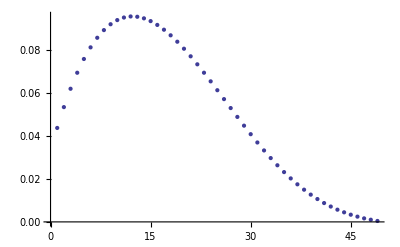

```mathematica
ListPlot[fwktc]
```

Now try just pure flicker noise:

```mathematica
flicker= 0.00001*filtNoise[premodo.stfo,flickCov[cyc]];
```

```mathematica
fflicker=matched[signal,flicker+onoise];
```

The optimum here is much more peaked:

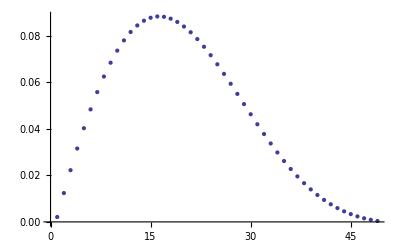

```mathematica
ListPlot[fflicker]
```

We can see that the optimum improves the signal to noise somewhat. First, the optimum:

```mathematica
snr[signal,fflicker,flicker+onoise]
```

236.298

Next, the signal with flicker noise filtered asssuming white and kTC noise:

```mathematica
snr[signal,fwktc,flicker+onoise]
```

216.296

```mathematica
snr[signal, fflicker, wktc+onoise]
```

179.461

```mathematica
snr[signal,fwktc,wktc+onoise]
```

242.824

```mathematica
snr[signal,fwktc,onoise]
```

1233.94

```mathematica
snr[signal,fflicker,onoise]
```

908.991

#### Optimizing the input filter

```mathematica
stff[j1v_,j2v_,j3v_,j4v_]=ks Cancel[(filter/.{j1->j1v,j2->j2v,j3->j3v,j4->j4v}/.tempa/.fb->0)/in]/(1+ks Cancel[(filter/.tempa/.in->0)/fb])/.ks->ke/.param/.coeff/.g12
```

(2.65962 (-j4v+j3v z+2.99817 j4v z-j2v z^2-1.99817 j3v z^2-2.99817 j4v z^2+j1v z^3+j2v z^3+j3v z^3+j4v z^3))/((1-1.99817 z+z^2) (1-1.9883 z+z^2) (1+(2.65962 (-0.366992+1.22138 z-1.36445 z^2+0.516382 z^3))/((1-1.99817 z+z^2) (1-1.9883 z+z^2))))

```mathematica
jsnr[j1_?NumberQ,j2_?NumberQ,j3_?NumberQ,j4_?NumberQ]:=Module[{stfi,stfo,flicker,fflicker,signal,r},
stfi=N[zToImpulse[stff[j1,j2,j3,j4],z,cyc]];
stfo=impulseToOperator[stfi,cyc];
signal=inputSignal.premodo.stfo;
flicker= 0.00001*filtNoise[premodo.stfo,flickCov[cyc]];fflicker=matched[signal,flicker+onoise];
r=snr[signal,fflicker,flicker+onoise];
r]
```

```mathematica
FindMaximum[{jsnr[j1,j2,j3,j4],j1≤0.36/64&&j2≤0.36/16&&j3≤0.36/4&&j4≤0.36&&j1>0&&j2>0&&j3>0&&j4>0},{{j1,0.005},{j2,0.02},{j3,0.08},{j4,0.3}},{AccuracyGoal->3,PrecisionGoal->3}]
```

{236.362,{j1→0.00562489,j2→0.0224991,j3→0.0899798,j4→0.000104627}}

```mathematica
jsnr[0.36/64,0.36/16,0.36/4,0]
```

236.363

Conclude that performance is insenstive to the j coefficients, keep them the same as the k’s.

### Resulting design

```mathematica
assump={c1->1/4,c2->1/4,c3->1/4,j1->k1,j2->k2,j3->k3,j4->k4}
```

{c1→1/4,c2→1/4,c3→1/4,j1→k1,j2→k2,j3→k3,j4→k4}

```mathematica
ffb=Cancel[(filter/.assump/.in->0)/fb]
```

(-64 k4+16 k3 z+192 k4 z-16 g1 k4 z-4 k2 z^2-32 k3 z^2+4 g1 k3 z^2-192 k4 z^2+16 g1 k4 z^2+k1 z^3+4 k2 z^3+16 k3 z^3+64 k4 z^3)/(4 (4-8 z+g1 z+4 z^2) (4-8 z+g2 z+4 z^2))

```mathematica
ntf=Together[1/(1+ke ffb)]
```

(4 √π (4-8 z+g1 z+4 z^2) (4-8 z+g2 z+4 z^2) σi)/(-64 √2 k4+16 √2 k3 z+192 √2 k4 z-16 √2 g1 k4 z-4 √2 k2 z^2-32 √2 k3 z^2+4 √2 g1 k3 z^2-192 √2 k4 z^2+16 √2 g1 k4 z^2+√2 k1 z^3+4 √2 k2 z^3+16 √2 k3 z^3+64 √2 k4 z^3+64 √π σi-256 √π z σi+16 g1 √π z σi+16 g2 √π z σi+384 √π z^2 σi-32 g1 √π z^2 σi-32 g2 √π z^2 σi+4 g1 g2 √π z^2 σi-256 √π z^3 σi+16 g1 √π z^3 σi+16 g2 √π z^3 σi+64 √π z^4 σi)

```mathematica
g12=(Solve[b CoefficientList[Numerator[ntf/.param],z]==Chop[CoefficientList[(z-Exp[I ϕ1])(z-Exp[-I ϕ1])(z-Exp[I ϕ2])(z-Exp[-I ϕ2])/.ϕ1->Pi/oversamp ϑ1/.ϕ2->Pi/oversamp ϑ2/.param,z]],{g1,g2},{b}]//Quiet)[[1]]
```

{g1→0.00730082,g2→0.0467911}

We’ve decided to leave out the resonator feedback this time, so the “g” coefficients are zero.

```mathematica
g12={g1->0,g2->0}
```

{g1→0,g2→0}

```mathematica
coeff=Solve[CoefficientList[Denominator[ntf/.param/.g12],z]==a Chop[CoefficientList[Times@@(1-z/ntfPoles/.param),z]],{k1,k2,k3,k4},{a}][[1]]
```

{k1→0.404543,k2→0.362669,k3→0.501946,k4→0.366992}

```mathematica
modulator[in_][state[n_,v_,{q1_,q2_,q3_,q4_},out_]]:=
Module[{nq1,nq2,nq3,nq4,nv,fb},
fb=-b2q[out];
nv=in[n];
nq1=q1+j1 nv+k1 fb-g1 q2;
nq2=q2+j2 nv+k2 fb+c1 nq1;
nq3=q3+j3 nv+k3 fb+c2 nq2-g2 q4;
nq4=q4+j4 nv+k4 fb+c3 nq3;
state[n+1,nv,{nq1,nq2,nq3,nq4},q2b[nq4]]]/.assump/.coeff/.g12
```

```mathematica
runf=Table[testrun[100./4096,1.,0.,modulator,12,49],{10000}];
```

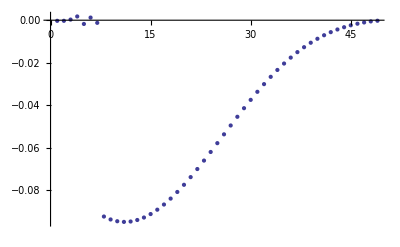

```mathematica
ListPlot[filtf= bestFilt[runf]]
```

```mathematica
1/RootMeanSquare[resid[runf,filtf]]
```

3375.37

```mathematica
1.2%
```

4050.44

```mathematica
runfx=Table[testrun[100./4096,1.6,0.,modulator,12,49],{10000}];
```

```mathematica
ListPlot[Transpose[{chg[runfx],resid[runfx,filtf]}],PlotRange->{-0.01,0.01}]
```

```mathematica
ListPlot[Transpose[{chg[runfx],bitmat[runfx].filtf}],PlotRange->All]
```

```mathematica
Max/@Transpose[getIntern/@runMod[modulator,(0.6)&,{0.,0.,0.,0.},1000]]
```

{0.783516,0.887849,0.956095,0.99357}

```mathematica
Min/@Transpose[getIntern/@runMod[modulator,(-0.6)&,{0.,0.,0.,0.},1000]]
```

{-0.658149,-0.728969,-0.762583,-0.812355}

### Sensitivity analysis

Perturb parameter p in rules by factor f:

```mathematica
perturb[rules_, p_, f_]:=rules/.(p->n_)->(p->f*n)
```

Example:

```mathematica
coeff
```

{k1→0.404543,k2→0.362669,k3→0.501946,k4→0.366992}

```mathematica
perturb[coeff,k1,1.1]
```

{k1→0.444997,k2→0.362669,k3→0.501946,k4→0.366992}

Do a perturbed run:

```mathematica
pertrun[trp_List,pert_List,n_]:= Block[{coeff=perturb@@pert},Table[testrun@@trp,{n}]]
```

Plot a perturbed run. Here, we’ll use the decimation filter from the linear algebra analysis. This yields slightly different gain and offset than the fitted filter, so the residuals will be a little off.

```mathematica
ppr[p_,f_]:=With[{run=pertrun[{0.03,1.2,0.001,modulator,12,49},{coeff,p,f},1000]},ListPlot[Transpose[{chg[run],resid[run,-fwktc]}],PlotRange->All]]
```

First, no perturbation:

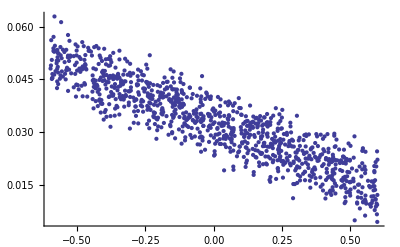

```mathematica
ppr[k1,1]
```

Increase k1 by 50%:

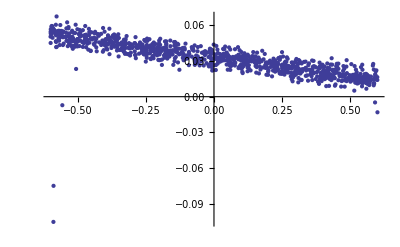

```mathematica
ppr[k1,1.5]
```

A few outliers around -0.6 demonstrate that we’ve degraded the stable range slightly, but it still looks OK.

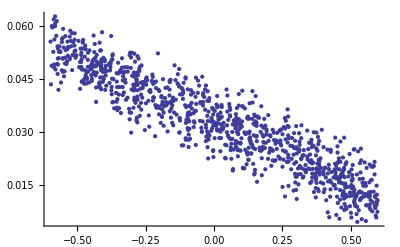

```mathematica
ppr[k1,0.5]
```

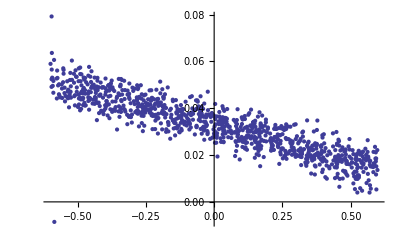

```mathematica
ppr[k2,1.5]
```

Again, a little instability, but not serious.

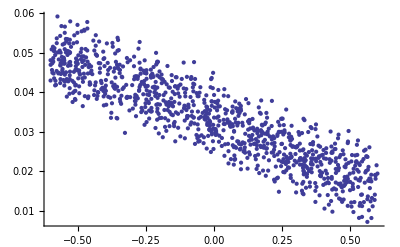

```mathematica
ppr[k2,0.5]
```

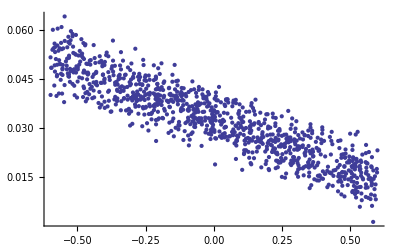

```mathematica
ppr[k3,1.5]
```

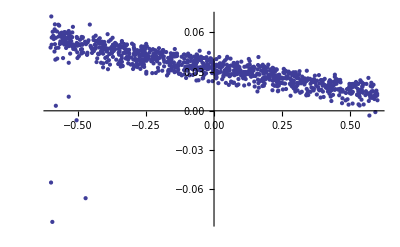

```mathematica
ppr[k3,0.5]
```

This is worse than the others, but still not bad.

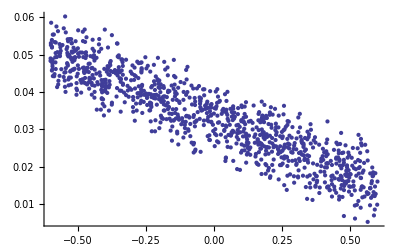

```mathematica
ppr[k4,1.5]
```

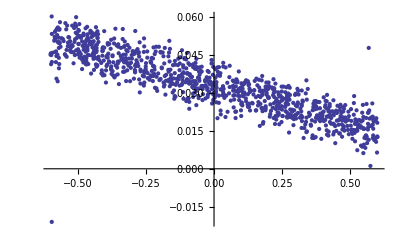

```mathematica
ppr[k4,0.5]
```

Conclusion: 50% changes in feedback coefficients do not seriously affect performance. Sensitivity of the design is low. This suggests a new strategy: make all the k coefficients the same.

```mathematica
meank= Mean[{k1,k2,k3,k4}/.coeff]
```

0.409038

```mathematica
coeff= {k1->0.4,k2->0.4,k3->0.4,k4->0.4};
```

```mathematica
runeq=Table[testrun[0.03,1.0,0.001,modulator,12,49],{10000}];
```

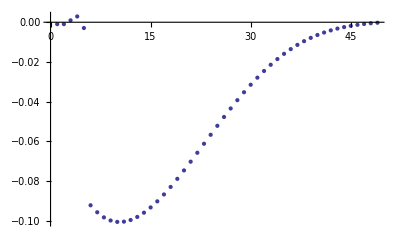

```mathematica
ListPlot[filteq = bestFilt[runeq]]
```

```mathematica
1/RootMeanSquare[resid[runeq,filteq]]
```

1143.19

```mathematica
runeqx=Table[testrun[0.03,1.6,0.001,modulator,12,49],{10000}];
```

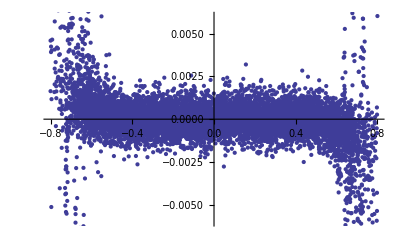

```mathematica
ListPlot[Transpose[{chg[runeqx],resid[runeqx,filteq]}],PlotRange->{-0.006,0.006}]
```

Go back to the "optimum" g = 0 coefficients :

```mathematica
coeff={k1->0.4045431606972619,k2->0.3626688279020913,k3->0.5019463419867609,k4->0.3669920389863944}
```

{k1→0.404543,k2→0.362669,k3→0.501946,k4→0.366992}

```mathematica
rung0=Table[testrun[0.03,1.0,0.001,modulator,12,49],{10000}];
```

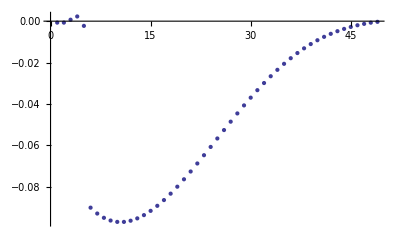

```mathematica
ListPlot[filtg0= bestFilt[rung0]]
```

```mathematica
1/RootMeanSquare[resid[rung0,filtg0]]
```

1604.69

OK, SNR is significantly better with optimum coefficients.

Try two digit precision.

```mathematica
coeff= {k1->0.4,k2->0.36,k3->0.5,k4->0.36};
```

```mathematica
run2d=Table[testrun[0.03,1.0,0.001,modulator,12,49],{10000}];
```

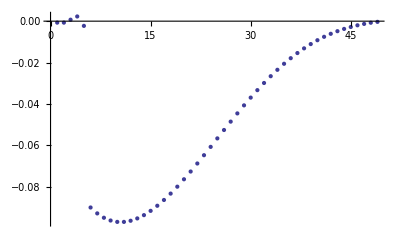

```mathematica
ListPlot[filt2d= bestFilt[run2d]]
```

```mathematica
1/RootMeanSquare[resid[run2d,filtg0]]
```

1653.81

Round numbers slightly better than “optimum” computed from BPAD!

So, we have coefficients of 0.25, 0.36, 0.40, and 0.50. For nice round capacitor values, make base value 200 fF, other values then are 50, 72, 80, and 100.